```mathematica
Graphics for Advanced Vector Calculus Notes
```

```mathematica
Plot[3x+9,{x, 0,6}, PlotStyle->{Pink,Thickness[0.01]}, PlotRange->{{0,10},{0,30}}]
```

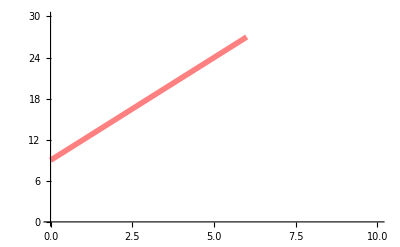

```mathematica
Plot3D[y=3*x+9, {x,0,6}, {y,9,27}, ColorFunction->"ValentineTones", ImageSize->Large]
```

-Graphics3D-

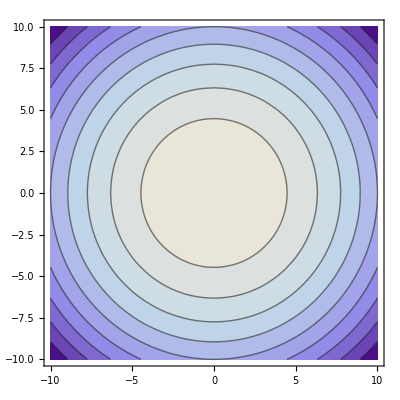

```mathematica
GraphicsRow[{Plot3D[-x^2-y^2, {x,-10,10}, {y,-10,10}, ColorFunction->"LakeColors", ImageSize->Full], ContourPlot[-x^2-y^2, {x,-10,10}, {y,-10,10}, ColorFunction->"LakeColors", ImageSize->Full]}]
```

```mathematica
Export["/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/paraboloid_3d.png",%89,"PNG"]
```

/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/paraboloid_3d.png

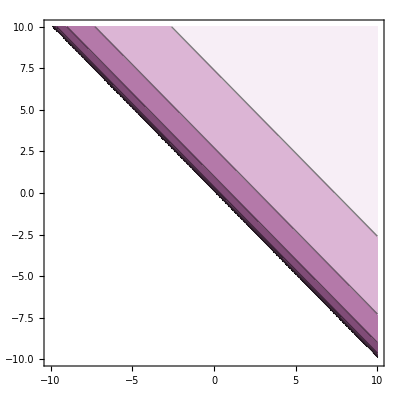

```mathematica
GraphicsRow[{Plot3D[Log[x+y], {x,-10,10}, {y,-10,10}, ColorFunction->"FuchsiaTones",  ImageSize->Full],ContourPlot[Log[x+y], {x,-10,10}, {y,-10,10}, ColorFunction->"FuchsiaTones",  ImageSize->Full]}]
```

```mathematica
Export["/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/logarithmic_3d.png",%92,"PNG"]
```

/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/logarithmic_3d.png

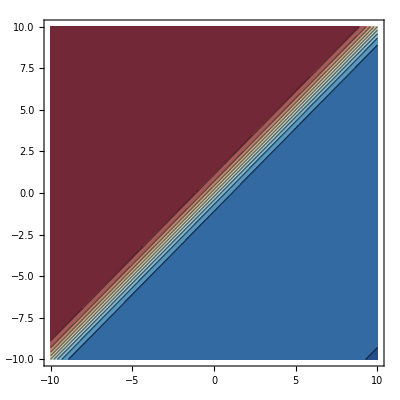

```mathematica
GraphicsRow[{Plot3D[Tanh[x-y], {x,-10,10}, {y,-10,10}, ColorFunction->"RedBlueTones",  ImageSize->Full],ContourPlot[Tanh[x-y], {x,-10,10}, {y,-10,10}, ColorFunction->"RedBlueTones",  ImageSize->Full]}]
```

```mathematica
Export["/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/hyperbolictangent_3d.png",%94,"PNG"]
```

/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/hyperbolictangent_3d.png

```mathematica
Export["/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/hyperbolictanget_3d.png",%94,"PNG"]
```

/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/hyperbolictanget_3d.png

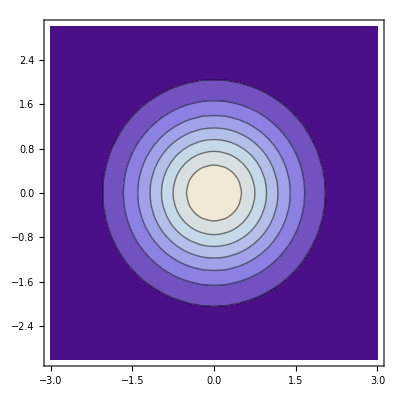

```mathematica
GraphicsRow[{Plot3D[PDF[MultinormalDistribution[{0,0},{{1,0},{0,1}}],{x,y}],{x,-3,3},{y,-3,3}, Mesh->50, ColorFunction->"LakeColors", ImageSize->Full],ContourPlot[PDF[MultinormalDistribution[{0,0},{{1,0},{0,1}}],{x,y}],{x,-3,3},{y,-3,3}, Mesh->70, ColorFunction->"LakeColors",ImageSize->Full]}]
```

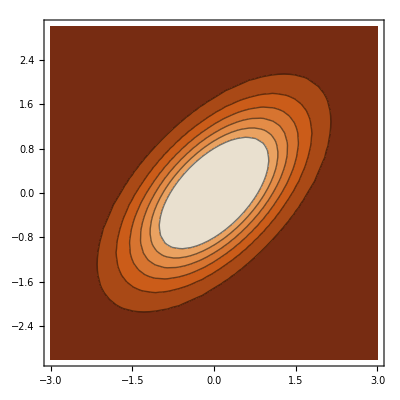

```mathematica
GraphicsRow[{Plot3D[PDF[MultinormalDistribution[{0,0},{{1,0.6},{0.6,1}}],{x,y}],{x,-3,3},{y,-3,3}, Mesh->50, ColorFunction->"SiennaTones", PlotRange->Full, ImageSize->Full],ContourPlot[PDF[MultinormalDistribution[{0,0},{{1,0.6},{0.6,1}}],{x,y}],{x,-3,3},{y,-3,3}, Mesh->70, ColorFunction->"SiennaTones", ImageSize->Full]}]
```

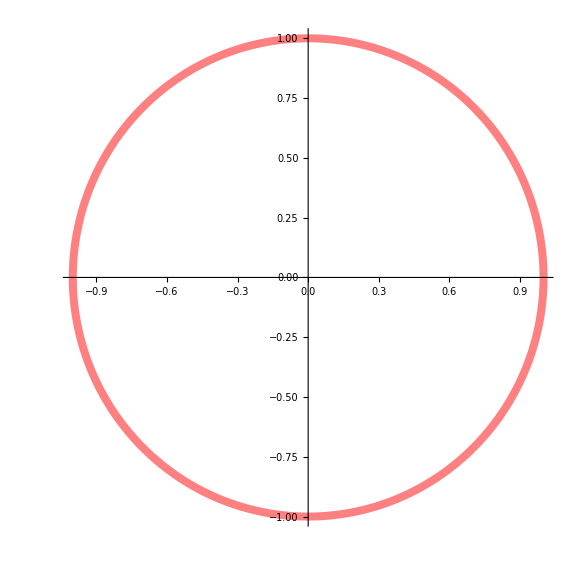

```mathematica
ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2*Pi}, PlotStyle->{Pink, Thickness[0.01]}, ImageSize->Large]
```

```mathematica
ArcLength[{Cos[t], Sin[t]}, {t, 0, 4*Pi}] // N
```

12.5664

```mathematica
ParametricPlot3D[{Cos[t], Sin[t], t}, {t, 0, 4*Pi}, PlotStyle->{Pink, Thickness[0.01]}, ImageSize->Large]
```

-Graphics3D-

```mathematica
ArcLength[{Cos[t], Sin[t], t}, {t, 0, 4*Pi}] // N
```

17.7715

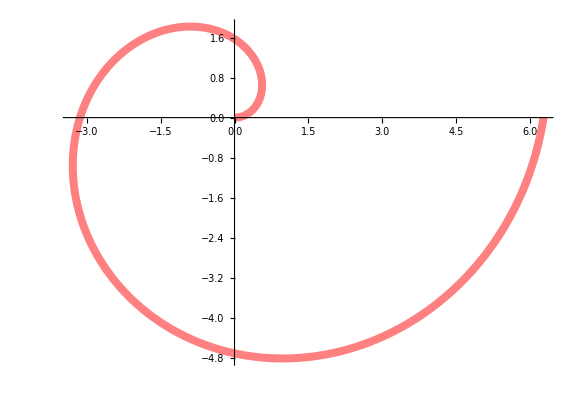

```mathematica
ParametricPlot[{t*Cos[t],t*Sin[t]},{t,0,2*Pi}, PlotRange->All, PlotStyle->{Pink, Thickness[0.01]}, ImageSize->Large]
```

```mathematica
ArcLength[{t*Cos[t],t*Sin[t]},{t,0,2Pi}]
```

π √(1+4 π^2)+1/2 ArcSinh[2 π]

```mathematica
ArcLength[{t*Cos[t],t*Sin[t]},{t,0,2Pi}] //N
```

21.2563

```mathematica
ParametricPlot3D[{t*Cos[t],t*Sin[t], t}, {t, 0, 12*Pi}, PlotStyle->{Pink, Thickness[0.01]}, ImageSize->Large]
```

-Graphics3D-

```mathematica
Plot3D[x*y,{x,0,1},{y,1,2}, RegionFunction->Function[{x,y,z},0<x<1&&1-x<y<1+x] ,ColorFunction->"CandyColors", Filling->Bottom, ImageSize->Large]
```

-Graphics3D-

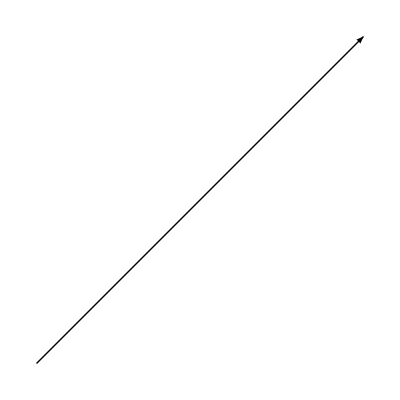

```mathematica
p1 = Graphics[Arrow[{{3,0},{4,1}}], DisplayFunction->Identity]
```

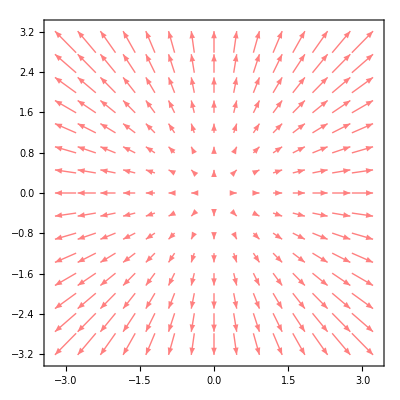

```mathematica
VectorPlot[{x,y},{x,-3,3},{y,-3,3}, VectorStyle->Pink]
```

{{2,-1},{4,-1},{4,3}}

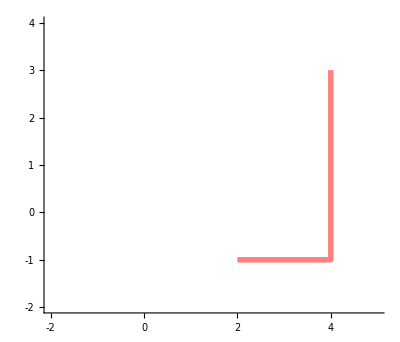

```mathematica
l = {{2,-1},{4,-1},{4,3}}
Graphics[{Pink,Thickness[0.01],Line[l]},Axes->True, PlotRange->{{-2,5},{-2,4}},Ticks->{{-2,-1,0,1,2,3,4,5},{-2,-1,0,1,2,3,4}}]
```

```mathematica
Plot3D[x*y,{x,0,1},{y,1,2}, ColorFunction->"CandyColors"]
```

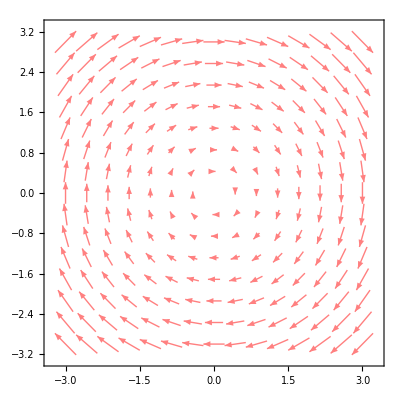

```mathematica
VectorPlot[{y,-x},{x,-3,3},{y,-3,3}, VectorStyle->Pink]

ParametricPlot[{-t,t},{t,-3,3}]
```

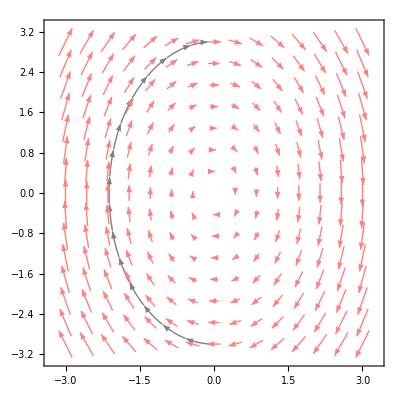

```mathematica
VectorPlot[{y,-x*2},{x,-3,3},{y,-3,3}, VectorStyle->Pink,StreamPoints->{{{{-2,-1},Gray}}}]
```

```mathematica
ContourPlot3D[x^2+y^2+z^2==4, {x,-3,3},{y,-3,3}, {z,-3,3}, ColorFunction->"MintColors"]
```

-Graphics3D-

```mathematica
Plot3D[x^2-y^2, {x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
Plot3D[-(x^2+y^2), {x,-10,10},{y,-10,10}, ColorFunction->"NeonColors"]
```

-Graphics3D-

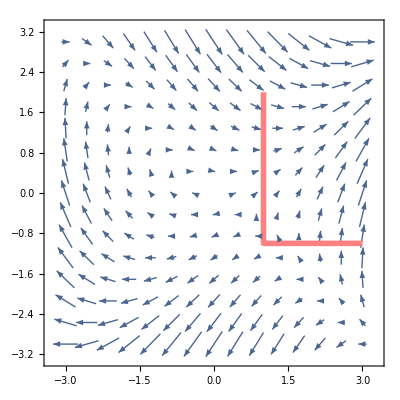

```mathematica
Show[VectorPlot[{x+2y,x^2-y^2},{x,-3,3},{y,-3,3}],
Graphics[{Pink,Thickness[0.01],Line[{{3,-1},{1,-1},{1,2}}]},Axes->True, PlotRange->{{-2,5},{-2,4}}]]
```

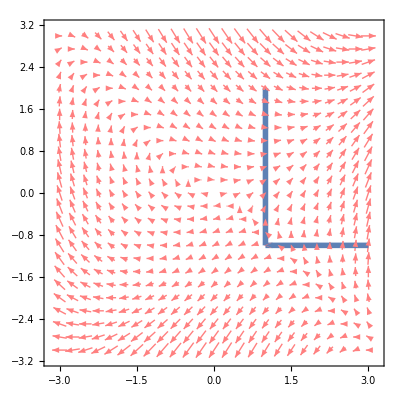

```mathematica
Show[VectorPlot[{x+2y,x^2-y^2},{x,-3,3},{y,-3,3}, VectorStyle->Pink, VectorPoints->Fine],
Graphics[{ColorData[97,"ColorList"][[1]], Thickness[0.01], Arrow[{{3,-1},{1,-1}}]}],
Graphics[{ColorData[97,"ColorList"][[1]], Thickness[0.01],  Arrow[{{1,-1},{1,2}}]}]
]
```

```mathematica
Export["/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/line_integral_example.png",%48,"PNG"]
```

/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/line_integral_example.png

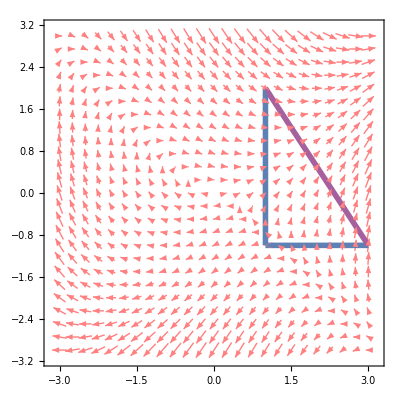

```mathematica
Show[VectorPlot[{x+2y,x^2-y^2},{x,-3,3},{y,-3,3}, VectorStyle->Pink, VectorPoints->Fine],
Graphics[{ColorData[97,"ColorList"][[1]], Thickness[0.01], Arrow[{{3,-1},{1,-1}}]}],
Graphics[{ColorData[97,"ColorList"][[1]], Thickness[0.01],  Arrow[{{1,-1},{1,2}}]}],
Graphics[{ColorData[97,"ColorList"][[9]], Thickness[0.01],  Arrow[{{3,-1},{1,2}}]}]
]
```

```mathematica
Export["/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/line_integral_example2.png",%73,"PNG"]
```

/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/line_integral_example2.png

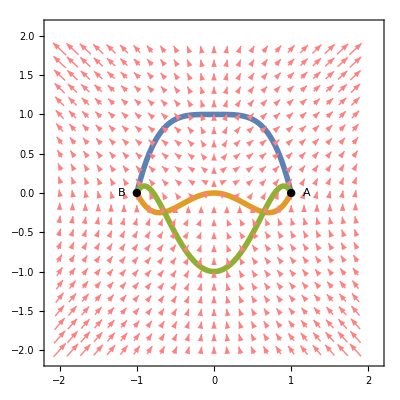

```mathematica
Show[VectorPlot[{x+6*x*y,3*y^2+3*x^2},{x,-2,2},{y,-2,2}, VectorStyle->Pink, VectorPoints->Fine],
Plot[1+-x^4,{x,-1,1}, PlotStyle->{Thickness[0.01],ColorData[97,"ColorList"][[1]]}],
Plot[x^4-x^2,{x,-1,1}, PlotStyle->{Thickness[0.01],ColorData[97,"ColorList"][[2]]}],
Plot[-1+2*x^2-x^6,{x,-1,1}, PlotStyle->{Thickness[0.01],ColorData[97,"ColorList"][[3]]}],
Graphics[{ PointSize[0.015],Point[{-1,0}]}],
Graphics[{Text["B",{-1.2,0}]}],
Graphics[{ PointSize[0.015],Point[{1,0}]}],
Graphics[{Text["A",{1.2,0}]}]
]
```

```mathematica
Export["/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/line_integral_example3.png",%207,"PNG"]
```

/Users/imad/Dropbox/Independent Study/Vector Calculus/Vector Calculus Notes/line_integral_example3.png

```mathematica
Integrate[7*t+2*t^11-24*t^7+6*t^5+12*t^3,{t,-1,1}]
```

0

```mathematica
Integrate[Dot[{1,4*t^3-2*t},{t+6*t*(t^4-t^2),3*(t^4-t^2)^2+3*t^2}],{t,-1,1}]
```

0